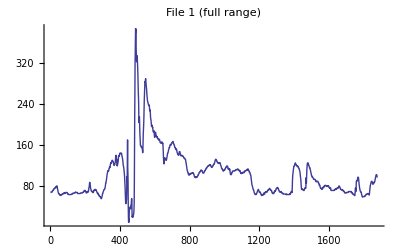
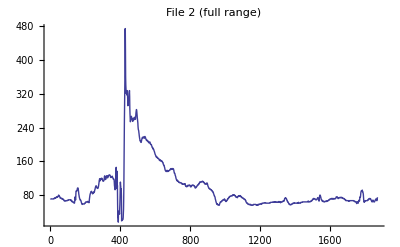
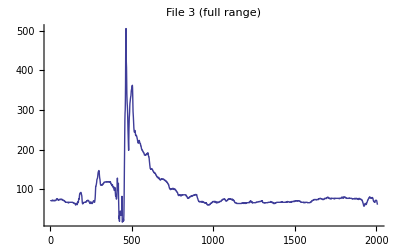
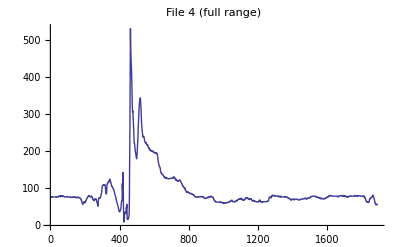
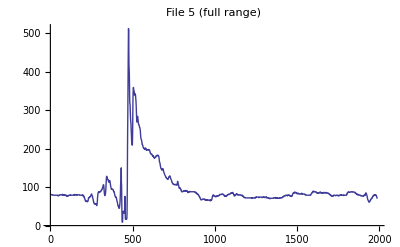
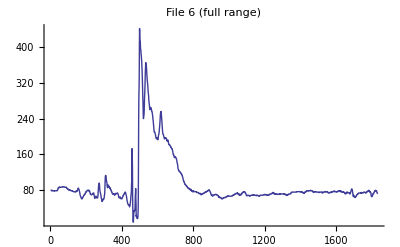
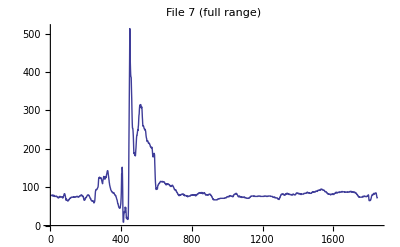
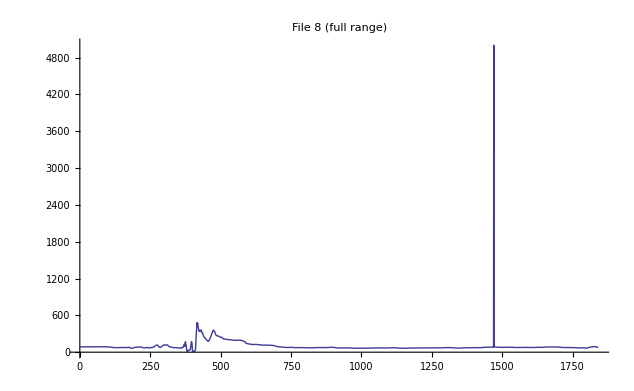

```mathematica
ClearAll[file,x,fle]
file=(Import["M:\\Proband1\\00506534Schluck2.ASC.data\\subset-max.csv","Data","HeaderLines"->0]);

Table[(
file=(Import["M:\\Proband1\\00506534Schluck"<>ToString[fle]<>".ASC.data\\subset-max.csv","Data","HeaderLines"->0]);
ListPlot[file[[All,2]],PlotLabel->StringJoin["File ",ToString[fle], " (full range)"], Joined->True,PlotRange->All]
),{fle,1,10}]

(*ParallelTable[ListPlot[file[[2,x]],PlotLabel->StringJoin["Column ",ToString[x], " (full range)"], Joined->True,PlotRange->All],{x,1,29}]*)
```